# Bifurcaciones en ecuaciones en diferencias

Tomemos la ecuación en diferencias

donde  es un parámetro.
Primero, veamos cómo cambia el lado derecho respecto a la identidad al variar el parámetro:

```mathematica
Manipulate[Plot[{x,Sin[w*x]},{x,-1.2,1.2},AxesLabel->{Subscript[x,n],Subscript[x,n+1]}],{w,0,2}]
```

Ahora veamos las soluciones para cada valor del parámetro.

## Caso

Las soluciones tienden exponencialmente a cero, por lo que el cero es una solución de equilibrio estable.

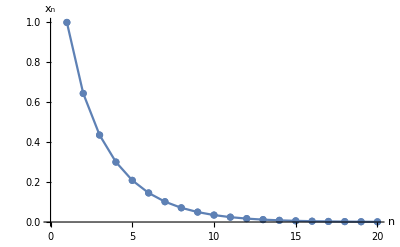

```mathematica
sol1=RecurrenceTable[{x[n+1]==Sin[0.7*x[n]],x[1]==1},x,{n,1,20}];
ListPlot[sol1,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True]
```

## Caso

Las soluciones tienden a cero como una ley de potencias, pero el cero sigue siendo estable. Estamos en el punto crítico de la bifurcación.

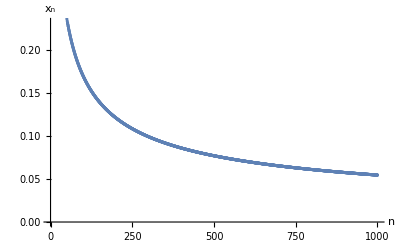

```mathematica
sol2=RecurrenceTable[{x[n+1]==Sin[x[n]],x[1]==1},x,{n,1,1000}];
ListPlot[sol2,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True]
```

## Caso

Las soluciones se alejan del cero y tienden a alguno de los dos puntos de equilibrio simétricos de manera monótona. El cero es inestable y los dos puntos de equilibrio adicionales son estables.

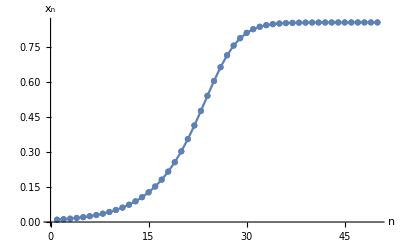

```mathematica
sol3=RecurrenceTable[{x[n+1]==Sin[1.2*x[n]],x[1]==0.01},x,{n,1,50}];
ListPlot[sol3,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True]
```

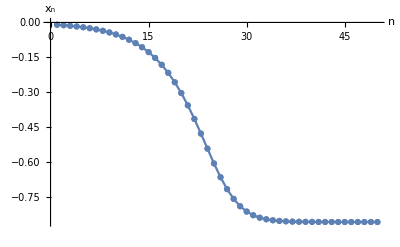

```mathematica
sol4=RecurrenceTable[{x[n+1]==Sin[1.2*x[n]],x[1]==-0.01},x,{n,1,50}];
ListPlot[sol4,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True]
```

## Caso

El cero sigue siendo inestable y los otros equilibrios estables, pero ahora las soluciones oscilan alrededor de ellos.

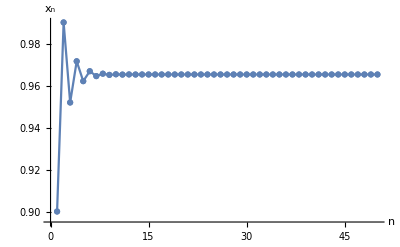

```mathematica
sol5=RecurrenceTable[{x[n+1]==Sin[1.9*x[n]],x[1]==0.9},x,{n,1,50}];
ListPlot[sol5,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True,PlotRange->All]
```

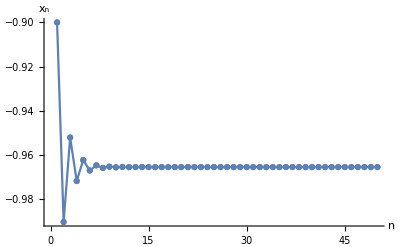

```mathematica
sol6=RecurrenceTable[{x[n+1]==Sin[1.9*x[n]],x[1]==-0.9},x,{n,1,50}];
ListPlot[sol6,Mesh->Full,AxesLabel->{n,Subscript[x,n]},Joined->True,PlotRange->All]
```

## Análisis de estabilidad lineal

Checamos de manera numérica que las dos soluciones adicionales sean estables después de que el cero se haga inestable, calculando la derivada y evaluándola en el punto de equilibrio para cada valor de .

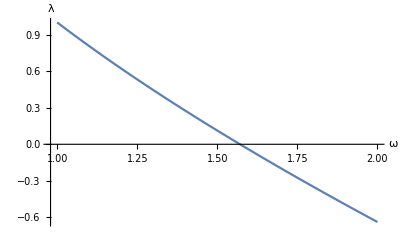

```mathematica
linearization=ParallelTable[{w,w*Cos[w*(x/.FindRoot[x==Sin[w*x],{x,1}])]},{w,1,2,0.01}];
ListPlot[linearization,AxesLabel->{ω,λ},Joined->True]
```

Vemos que siempre son estables cuando existen, porque el eigenvalor tiene valor absoluto menor a uno, pero a partir de 1.56 aproximadamente, se vuelve negativo, lo que indica la presencia de oscilaciones.
Con esta información podemos graficar el diagrama de bifurcación, recordando que graficamos con líneas punteadas los equilibrios inestables y con lineas continuas los equilibrios estables.

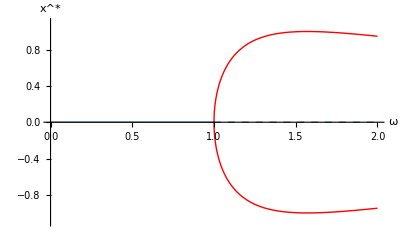

```mathematica
eqpos=ParallelTable[{w,x/.FindRoot[x==Sin[w*x],{x,1}]},{w,1,2,0.001}];
eqneg=ParallelTable[{w,x/.FindRoot[x==Sin[w*x],{x,-1}]},{w,1,2,0.001}];
Show[{Plot[0,{x,0,1},PlotStyle->Thick,AxesLabel->{ω,SuperStar[x]},PlotRange->{{0,2},{-1.1,1.1}}],Plot[0,{x,1,2},PlotStyle->{Dashed,Thick}],ListPlot[eqpos,Joined->True,PlotStyle->{Red,Thick},PlotRange->All],ListPlot[eqneg,Joined->True,PlotStyle->{Red,Thick},PlotRange->All]}]
```